## Data

```mathematica
localization=Import["D:\\Dropbox (ASU)\\DNA-PAINT Archive\\Bima DNA PAINT\\Data for Figure Manuscript\\Mathematica Plotting for Figure\\Figure 1\\dnapaintloc_longR1_normal_anneal_2.csv"];
```

## Using CDF Fitting to Fit the Data

## Plotting the CDF

```mathematica
yaxis=Range[0,1,1/Length[localization]];
```

```mathematica
dataplotcdf=Table[{localization⟦n,1⟧,yaxis⟦n⟧},{n,Length[localization]}];
```

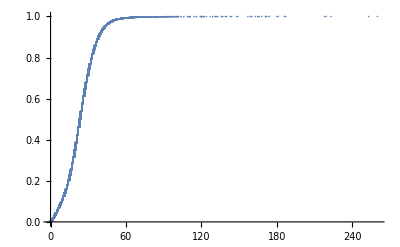

```mathematica
plotcdf=ListPlot[dataplotcdf, PlotRange->All]
```

## Fitting the CDF with a Gaussian Distribution CDF

From Wikipedia

-Graphics-

```mathematica
nlm=NonlinearModelFit[dataplotcdf, amp/2× (1+Erf[(x-μ)/(σ √2)]),{amp,μ,σ},x]
```

FittedModel[0.492566 (1+Erf[0.0658512 (-23.2784+x)])]

```mathematica
nlm["BestFitParameters"]
```

{amp→0.985132,μ→23.2784,σ→10.738}

```mathematica
nlm["RSquared"]
```

0.999735

## Plotting the Fit of the CDF

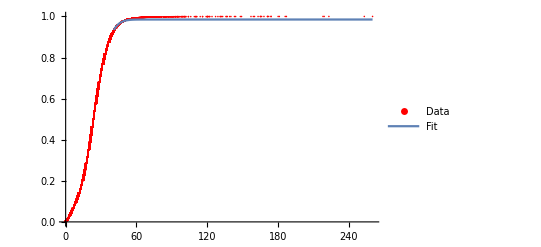

```mathematica
Show[ListPlot[dataplotcdf, PlotRange->All, PlotStyle->Red,PlotLegends->LineLegend[{"Data"}]],Plot[nlm[x],{x,0,Max[localization]},PlotLegends->LineLegend[{"Fit"}]]]
```

## Overlay Fitting Line with the Histogram (PDF)

```mathematica
datahistogram=Table[localization⟦i,1⟧,{i,Length[localization]}];
```

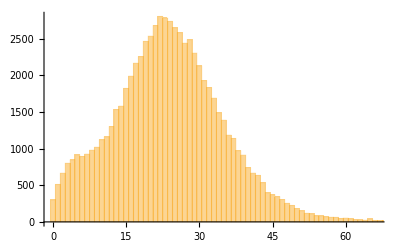

```mathematica
Histogram[{datahistogram},1000]
```

Gaussian PDF from Wikipedia

-Graphics-

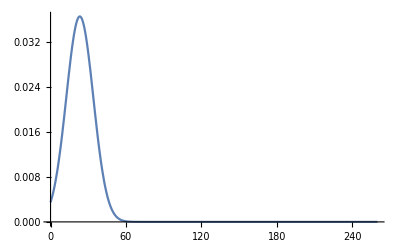

```mathematica
Plot[(nlm["BestFitParameters"]⟦1,2⟧)/(nlm["BestFitParameters"]⟦3,2⟧√(2π))Exp[-1/2((x-nlm["BestFitParameters"]⟦2,2⟧)/(nlm["BestFitParameters"]⟦3,2⟧))^2],{x,0,Max[localization]}, PlotRange->Full]
```

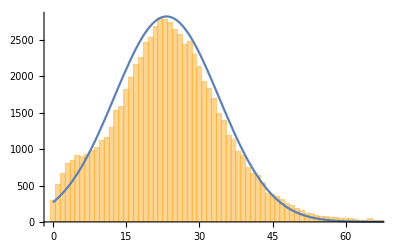

```mathematica
Show[Histogram[{datahistogram},1000],Plot[((10*7600)/(nlm["BestFitParameters"]⟦3,2⟧√(2π)))Exp[-(1/2)((x-nlm["BestFitParameters"]⟦2,2⟧)/nlm["BestFitParameters"]⟦3,2⟧)^2],{x,0,Max[localization]},PlotRange->All]]
```

```mathematica
ymax=(nlm["BestFitParameters"]⟦1,2⟧)/(nlm["BestFitParameters"]⟦3,2⟧√(2π))Exp[-1/2(0/(nlm["BestFitParameters"]⟦3,2⟧))^2]
```

0.0366002

```mathematica
halfymax=ymax/2
```

0.0183001

```mathematica
Solve[(nlm["BestFitParameters"]⟦1,2⟧)/(nlm["BestFitParameters"]⟦3,2⟧√(2π))Exp[-1/2((x-nlm["BestFitParameters"]⟦2,2⟧)/(nlm["BestFitParameters"]⟦3,2⟧))^2]==halfymax,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→10.6354},{x→35.9214}}

## Using MLE Estimation to Fit the Data

```mathematica
mle=EstimatedDistribution[datahistogram, NormalDistribution[α,β], ParameterEstimator->"MaximumLikelihood"]
```

NormalDistribution[23.9774,12.1744]

```mathematica
mle⟦1⟧
```

23.9774

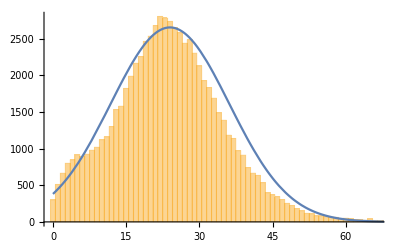

```mathematica
Show[Histogram[{datahistogram},320],Plot[((10*8100)/(mle⟦2⟧√(2π)))Exp[-(1/2)((x-mle⟦1⟧)/mle⟦2⟧)^2],{x,0,Max[localization]},PlotRange->All]]
```

```mathematica
ymaxmle=1/(mle⟦2⟧√(2π))Exp[-1/2(0/mle⟦2⟧)^2]
```

0.032769

```mathematica
halfymaxmle=ymaxmle/2
```

0.0163845

```mathematica
Solve[1/(mle⟦2⟧√(2π))Exp[-1/2((x-mle⟦1⟧)/mle⟦2⟧)^2]==halfymaxmle,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→9.64312},{x→38.3116}}

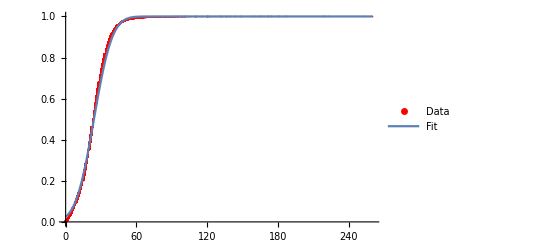

```mathematica
Show[ListPlot[dataplotcdf, PlotRange->All, PlotStyle->Red,PlotLegends->LineLegend[{"Data"}]],Plot[CDF[mle,x],{x,0,Max[localization]},PlotRange->All,PlotLegends->LineLegend[{"Fit"}]]]
```